## Testing Caching Animations

```mathematica
Clear["Global`*"]
```

```mathematica
PacletManager`PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< SimulationFunctions`
```

```mathematica
<< PlotFunctions`
```

```mathematica
Function[{x,y}, 1/((2^(1+1)π)^(1/4))Exp[-x^2/2] HermiteH[1, x] Exp[-y^2/2] HermiteH[1, y]Exp[-ⅈ x/5]];
Function[{x, y}, 1/2(x^2+y^2)];

wavef = EvolveWavefunction[%%, %, {-5, 5}, {-5, 5}, 1];
```

```mathematica
frames = Table[
					PlotWavefunction[
						(wavef[#1, #2, t]&), {-3, 3}, {-3, 3},
						ShowBar -> False,
						PlotRange -> {0, .2},
						Potential -> (#1^2/20 + #2^2/20 &),
						PointsActivePassive -> {30, 50}
					],
					{t, 0, 1, 0.1}
				];
```

```mathematica
ListAnimate[frames, 10]
```

```mathematica
DynamicModule[
	{va, vp, vv},
	va = 60 Degree;
	vp = {1, 1, 1};
	vv = {0, 0, 1};

	frames2 = Table[
					Plot3D[
						Abs[wavef[x, y, t]]^2, {x, -3, 3}, {y, -3, 3},
						PlotRange -> {0, .2},
						PlotPoints -> ControlActive[30, 50],
						
						ViewAngle -> Dynamic@va,
						ViewPoint -> Dynamic@vp,
						ViewVertical -> Dynamic@vv
					],
					{t, 0, 1, 0.1}
				];
	];
```

```mathematica
ListAnimate[frames2]
```

passing on args test

```mathematica
Options[fouter] = {
	innerargs -> {}
};

fouter[OptionsPattern[]] :=
	finner[ Sequence @@ OptionValue[innerargs]];
```

```mathematica
fouter[innerargs -> {a -> 1, b -> 2, c -> 3}]
```

finner[a→1,b→2,c→3]

```mathematica
Clear[finner, fouter]
```

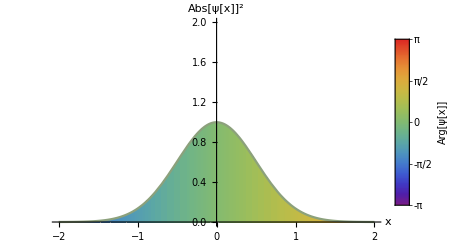

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[<|a→9|>,{a}].

Take[<|a→9|>,{a}]

```mathematica
PlotWavefunction[
	Exp[-x^2] Exp[ⅈ x], 
	{x, -2, 2},
	PlotRange -> {0, 2},
	PlotOptions -> {Mesh -> All}
]
```